# Teaching Trigonometry, Geometry, and Calculus at the Same Time

Abe Gadalla

In this Notebook, examples of teaching one concept through four different approaches...

## Trigonometry

Calculate the area among curves using geometrical knowledge...

### Subsection. Trigonometric Construction for Finding Red Area

Explain this...

```mathematica
sol1Step1=Graphics[{
{EdgeForm[{Thick,Black}],
FaceForm[{Red,Opacity[0.85]}],
DiskSegment[{0,0},1,{π/6,Pi/3}],,
DiskSegment[{1,0},1,{2π/3,5Pi/6}],
DiskSegment[{0,1},1,{5π/3,11Pi/6}],
DiskSegment[{1,1},1,{7π/6,4Pi/3}]},
{EdgeForm[{Thick,Red}],FaceForm[Yellow],Polygon[{{0,0},{0.5,(√3)/2},{(√3)/2,0.5}}]},{Black,Arrow[{{0,0},{(√3 + 1)/4, (√3 +1)/4}}]},
{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]}}]
```

-Graphics-

### Subsection. Constructing Labels

Label the coordinates of the points and the length of the base of the triangle and measure of angles.

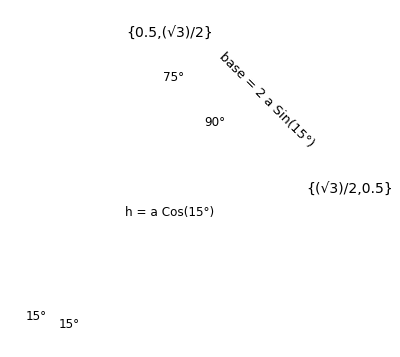

```mathematica
sol1Step2 = Graphics[{Inset [Style[TraditionalForm[{(√3)/2 , 0.5 }], 14,Black],{(√3)/2 +0.12, 0.51 }],Inset[Style["{0.5,(√3)/2}",14,Black],{0.5,(√3)/2+0.05}],Inset[Style["90°" ,12,Black],{(√3 + 1)/4-0.06, (√3 +1)/4}],Inset[Style["75°" ,12,Black],{0.51,0.8}],
Inset[Style["15°" ,12,Black],{0.23,0.16}],Inset[Style["15°" ,12,Black],{0.14,0.18}],Inset[Style["h = a Cos(15°)" ,12,Black],{0.5,0.45}],Inset[Rotate[Style["base = 2 a Sin(15°)" ,13,Black],-π/4,{0,0}],{0.76,0.74}]}]
```

### Subsection. Combine Steps 1 and 2

```mathematica
trigsolution1= Show [main,sol1Step1,sol1Step2]
```

-Graphics-

## Another Approach for Trigonometric Solution

### Subsection. Trigonometric Construction for Finding Red Area

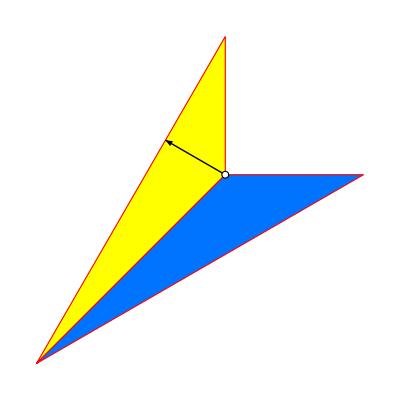

```mathematica
sol2Step1=Graphics[{
{EdgeForm[{Thick,Red}],FaceForm[Yellow],Polygon[{{0,0},{0.5,(√3)/2},{0.5,0.5}}]},{EdgeForm[{Thick,Red}],FaceForm[RGBColor[0,0.45,1]],Polygon[{{0,0},{0.5,0.5},{(√3)/2,0.5}}]},{Black,Arrow[{{0.5,0.5},{(√3 + 1)/8, (3 +√3)/8}}]},
{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]}}]
```

### Subsection. Constructing Labels

Coordinates of the intersection points as well as angles.

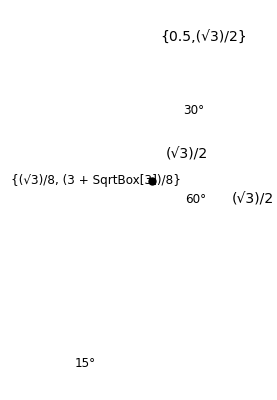

```mathematica
plot2 = Plot[{√(1-x^2) ,0.5},{x,0.5,(√3)/2},Filling->{1->{2}},FillingStyle->Directive[Red,Opacity[0.85]]];
sol2Step2 = Graphics[{Inset [Style[" (√3)/2", 14,Black],{0.65,0.55}],PointSize[0.015],Point[{(√3 + 1)/8, (3 +√3)/8}],Inset[Style["{(√3)/8, (3 + SqrtBox[3])/8}",12,Black],{(√3 + 1)/8-0.17, (3 +√3)/8}],Inset[Style["{0.5,(√3)/2}",14,Black],{0.5,(√3)/2+0.05}],Inset[Style["30°" ,12,Black],{0.47,0.75}],Inset[Style["60°" ,12,Black],{0.475,0.55}],Inset[Style["15°" ,12,Black],{0.14,0.18}],Inset[Style["(√3)/2" ,14,Black],{0.45,0.65}]}]
```

### Subsection. Combine Steps 1 and 2

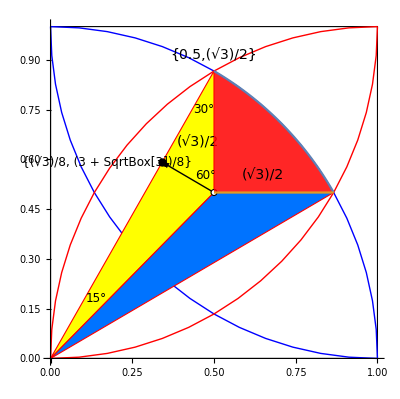

```mathematica
trigsolution2 = Show [main,sol2Step1,plot2,sol2Step2]
```

## Geometry

Calculate the area among curves using geometrical knowledge...

### Step 1: Calculating the area of the red crescent:

Subtract the area of the equilateral triangle from the area of the sector whose angle is π/3.

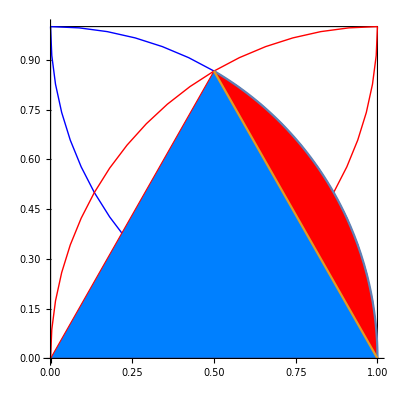

```mathematica
main=Graphics[{{EdgeForm[{Black,Thick}],FaceForm[White],Rectangle[{0,0},{1,1}]},{Thick,Blue,Circle[{1,1},1,{π,3π/2}],Circle[{0,0},1,{0,π/2}]},{Thick,Red,Circle[{1,0},1,{π/2,π}]},{Thick,Red,Circle[{0,1},1,{3π/2,2π}]}
},Axes->True,AxesOrigin->{0,0}];
triangle = Graphics[{{EdgeForm[{Thick,Red}],FaceForm[RGBColor[0,0.5,1]],Polygon[{{0,0},{0.5,√3/2},{1,0}}]}}];
cresentR=Plot[{√(1-(x)^2), -√3(x-1)},{x,0.5,1},Filling->{1->{2}},FillingStyle->Red];
Show[main,triangle,cresentR,PlotRange->All]
```

### Step 2: Calculating the remaining yellow area

### Add the area of the sector to the area of a cresent and subtract the result from the area of the quarter circle.

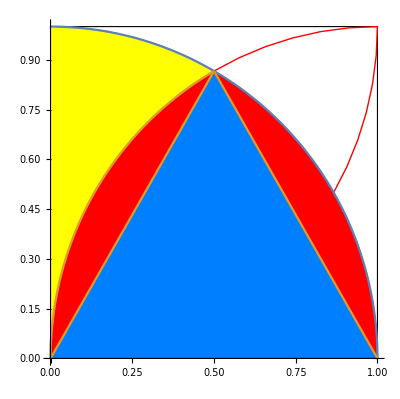

```mathematica
triangle = Graphics[{{EdgeForm[{Thick,Red}],FaceForm[RGBColor[0,0.5,1]],Polygon[{{0,0},{0.5,√3/2},{1,0}}]}}];
cresentL=Plot[{√(1-(x-1)^2), √3 x},{x,0,0.5},Filling->{1->{2}},FillingStyle->Red];
cresentR=Plot[{√(1-(x)^2), -√3(x-1)},{x,0.5,1},Filling->{1->{2}},FillingStyle->Red];
yellowAreaL=Plot[{√(1-x^2),√(1-(x-1)^2)},{x,0,0.5},Filling->{1->{2}},FillingStyle->Directive[Yellow,Opacity[1]]];
Show[main,triangle,cresentR,cresentL,yellowAreaL,PlotRange->All]
```

### Step 3: Subtract four times the yellow area from the area of the square to obtain the required shaded area

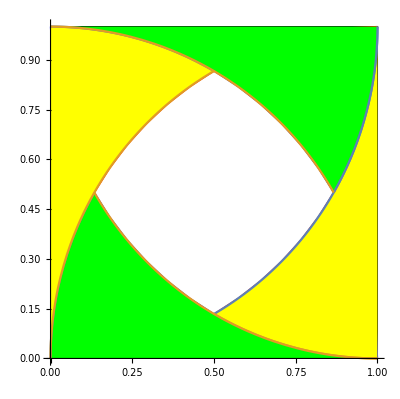

```mathematica
yellowAreaR=Plot[{1-√(1-x^2),1-√(1-(x-1)^2)},{x,0.5,1},Filling->{1->{2}},FillingStyle->Yellow];
GreenAreaTop1=Plot[{1,√(1-x^2)},{x,0,√3/2},Filling->{1->{2}},FillingStyle->Green];
GreenAreaTop2=Plot[{1,1-√(1-x^2)},{x,√3/2,1},Filling->{1->{2}},FillingStyle->Green];
GreenAreaBottom1=Plot[{1-√(1-(x-1)^2)},{x,1-√3/2,1},Filling->Axis,FillingStyle->Green];
GreenAreaBottom2=Plot[{√(1-(x-1)^2)},{x,0,1-√3/2},Filling->Axis,FillingStyle->Green];

yellowAreasT=Graphics[{Rotate[yellowAreaL[[1]]/.Yellow->Green,π/2,{0.5,0.5}]}];
YellowT=Graphics[{Rotate[yellowAreaL[[1]]/.Yellow->Green,3π/2,{0.5,0.5}]}];
Show[main,yellowAreaR,yellowAreasT,yellowAreaL,YellowT,PlotRange->All]
```

### Summary of solution

Subtract the shaded areas (2 yellow and 2 green ) from the area of the square to obtain the required area.

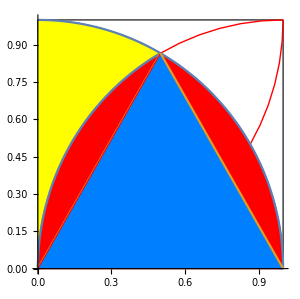
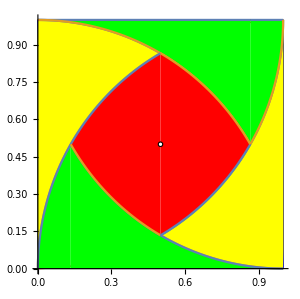

```mathematica
Row[
{
Show[main,geometricsolution,ImageSize->300],
Spacer[30],
Show[main,finalgeometricsolution,ImageSize->300]
}
]
```

## Integration

Solution by Integration...

### Subsection. Construction of Left and Right Halves of Shaded Area

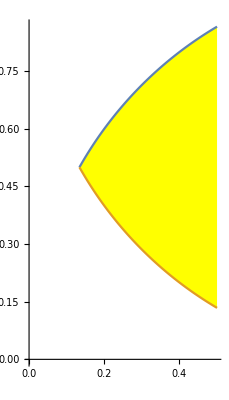

```mathematica
LeftPart=Plot[{√(2 x-x^2),1-√(2 x-x^2)},{x,1-(√3)/2,1/2},Filling->{1->{2}},FillingStyle->Yellow,AspectRatio->Automatic,Axes->True,AxesOrigin->{0,0}]
```

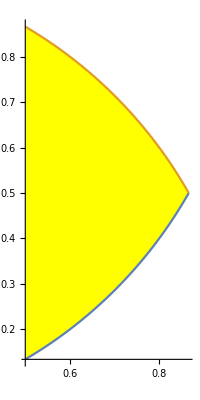

```mathematica
RightPart=Plot[{1-√(1-x^2),√(1-x^2)},{x,1/2,(√3)/2},Filling->{1->{2}},FillingStyle->Yellow,AspectRatio->Automatic]
```

### Subsection. Rectangular Slice Required for Integration

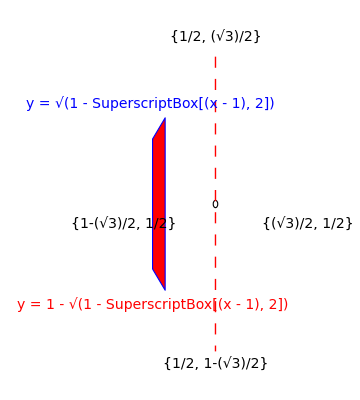

```mathematica
graphIntg=Graphics[{EdgeForm[{Thick,Blue}],FaceForm[Red],Polygon[{{0.25,1-√(0.5- 0.0625)},{0.25,√(0.5-0.25^2)},{0.3,√(0.6- (0.3)^2)},{0.3,1-√(0.6-0.3^2)}}],{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]},{Red,Dashing[0.02],Line[{{1/2, (√3)/2},{1/2, 1-(√3)/2}}]},Inset[Style["{1/2, (√3)/2}",14,Black],{0.5,(√3)/2+0.05}],Inset[Style["{1/2, 1-(√3)/2}",14,Black],{0.5,1-(√3)/2-0.03}],Inset[Style["{1-(√3)/2, 1/2}",14,Black],{1-(√3)/2,0.45}],
Inset[Style["{(√3)/2, 1/2}",14,Black],{(√3)/2,0.45}],
Inset[Style["y = √(1 - SuperscriptBox[(x - 1), 2])",14,Blue],{0.24,0.75}],
Inset[Style["y = 1 - √(1 - SuperscriptBox[(x - 1), 2])",14,Red],{0.25,0.25}]
}]
```

Compute the exact area via integration

```mathematica
YellowArea = 2 ∫_(1-(√3)/2)^(1/2) (√(1-(x-1)^2)-(1 - √(1-(x-1)^2)))ⅆx
```

1/3 (3-3 √3+π)

### Subsection. Display the Solution

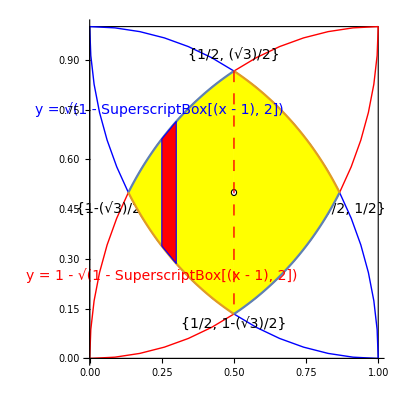

```mathematica
integrationsolution=Show[main,LeftPart,RightPart,graphIntg,PlotRange->All]
```

## Combine Solutions Into a Manipulate

```mathematica
Manipulate[
Column[{
Item[If[answer,Text@Style[Row[{"\nShaded Area = ",NumberForm[RequiredAreaSqr,{5,3}]," cm^2 \nOr By Integration: Area = ",HoldForm[ 2 (∫_(1-(√3)/2)^(1/2) (√(1-(x-1)^2)-(1 - √(1-(x-1)^2)))ⅆx)]," = ",YellowAreaSqr,"\n"}],14,Black],
Text@Style["\nCalculate the shaded Area, given that the side length\n of the square is 1 cm \n",14,Black]
],
Frame->True,Alignment->Left
],

Item[
Which[
sol==0,Show[main,Leftshade,Rightshade,ImageSize->400],
sol==1,Show [main,sol1Step1,sol1Step2,ImageSize->400],
sol==2, Show [main,sol2Step1,plot2,sol2Step2,ImageSize->400],
sol==3,Row[{
Show[main,geometricsolution,ImageSize->400],Spacer[30],
Show[main,finalgeometricsolution,ImageSize->400] }],
True,
Show[main,LeftPart,RightPart,graphIntg,ImageSize->400,PlotRange->All]
],
Frame->True,Alignment->{Center}
]
}
],

Row[
{
Control[{{sol,0,"Problem"},{0->"",1->"Trig Solution 1",2->"Trig Solution 2",3->"Geometric Solution",4->"Integration Solution"},ControlType->RadioButtonBar}],
Spacer[21],
Control[{{answer,False,"Answer"},{False,True}}]
}
],
TrackedSymbols:>{sol,answer},
SaveDefinitions->True
]
```

Show::gcomb: Could not combine the graphics objects in Show[main,LeftPart,RightPart,graphIntg,ImageSize→400,PlotRange→All].

## Code

Initialization code that is run before other code is evaluated:

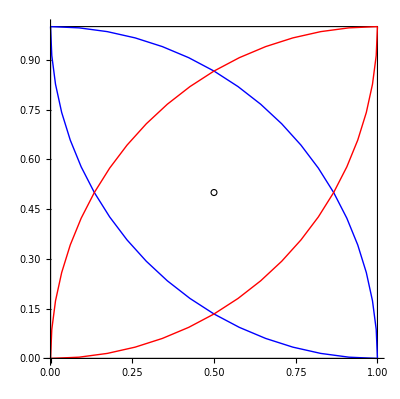

```mathematica
main=Graphics[{{EdgeForm[{Black,Thick}],FaceForm[White],Rectangle[{0,0},{1,1}]},{Blue,Circle[{1,1},1,{π,(3 π)/2}],Circle[{0,0},1,{0,π/2}]},{Red,Circle[{1,0},1,{π/2,π}]},{Red,Circle[{0,1},1,{(3 π)/2,2 π}]},{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},.009]}},Axes->True,AxesOrigin->{0,0}]
```

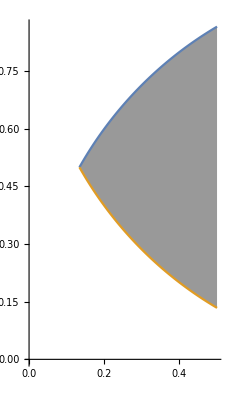

```mathematica
Leftshade=Plot[{√(2 x-x^2),1-√(2 x-x^2)},{x,1-(√3)/2,1/2},Filling->{1->{2}},FillingStyle->GrayLevel[0.6],AspectRatio->Automatic,Axes->True,AxesOrigin->{0,0}]
```

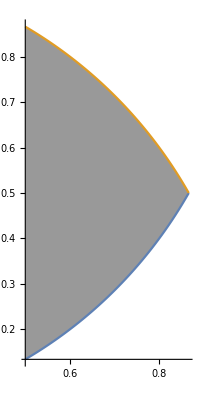

```mathematica
Rightshade=Plot[{1-√(1-x^2),√(1-x^2)},{x,1/2,(√3)/2},Filling->{1->{2}},FillingStyle->GrayLevel[0.6],AspectRatio->Automatic]
```

```mathematica
areaSeg=π/(2 6.);
```

```mathematica
areaTriangle=N[Sin[π/12] Cos[π/12]]
```

0.25

```mathematica
RedAreas=4.(areaSeg - areaTriangle)
```

0.0471976

```mathematica
RequiredAreaSqr=RedAreas+(2 Sin[π/12])^2
```

0.315147

```mathematica
YellowAreaSqr=2 ∫_(1-(√3)/2)^(1/2) (√(1-(x-1)^2)-(1-√(1-(x-1)^2)))ⅆx
```

1/3 (3-3 √3+π)

## exercise

```mathematica
y1=√(2 x -x^2);
y2=1-√(1 -x^2);
y3=√(1-x^2);
y4=1-√(2 x-x^2);
ShadedArea2:=FullSimplify[ 2. (∫_(1-(√3)/2)^(1/2) (√(1-(x-1)^2)-(1 - √(1-(x-1)^2)))ⅆx)]-π (1-√2/2.)^2;

fp1=Plot[{y1,y4},{x,1-(√3)/2,1/2},Filling->{1->{2}},FillingStyle->Gray,AxesOrigin->{0,0},Axes->False,PlotLabel->Style["\nCalculate the shaded area\n",24,Italic,Black]];
g1=Graphics[{{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},0.01]},{Thick,Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]}}];
g2=Graphics[{{EdgeForm[{Thick,Black}],FaceForm[White],Disk[{0.5,0.5},1-√2/2.]},{Red,PointSize[0.025],Point[{0.5,0.5}]}(*{Thick,Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]}*)}];
fp2=Plot[{y3,y2},{x,1/2,(√3)/2},Filling->{1->{2}},FillingStyle->Gray];
p1=Plot[{y1,y2},{x,0,1},PlotStyle->{{Thickness[0.01],RGBColor[1,0,0]}}];
p2=Plot[{y3,y4},{x,0,1},PlotStyle->{{Thickness[0.01],RGBColor[0,0,1]}}];
Manipulate[Column[{
Item[If[answer,Style[Row[{"\nShaded area = ", NumberForm[ShadedArea2,{4,2}]," cm^2\n"}],24,Black],Style["\nCalculate the shaded area\n",24,Italic,Black]],Alignment->{Left},Frame->True],
Item[
Show[fp1,fp2,p1,p2,g2,PlotRange->All,AspectRatio->Automatic,ImageSize->{450,400}],Alignment->{Center},Frame->True]
}],
{{answer,False,"Answer"},{False,True}},TrackedSymbols->{answer}]
```